# Mean Shift Clustering

## Generate Random data

```mathematica
SeedRandom[4]
pts={};
numPts=800;
For[i=1,i≤numPts,i++,
AppendTo[pts,{RandomVariate[NormalDistribution[1,3]],RandomVariate[NormalDistribution[1,1.8]]}]
];
```

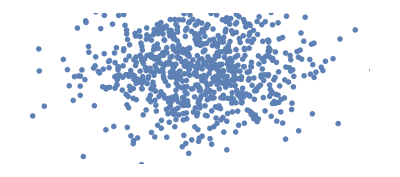

```mathematica
ListPlot[pts,PlotStyle->PointSize[0.01],Ticks->None,Axes->None,AspectRatio->8/18,PlotRange->{{-8,10},{-4,4}}]
```

## Place 5 windows at random positions

```mathematica
centers={};
windowSize=1.5;
numCenters=5;
For[i=1,i≤numCenters,i++,
AppendTo[centers,{RandomReal[{-8,8}],RandomReal[{-3,3}]}]
];
```

## Plot the initial windows

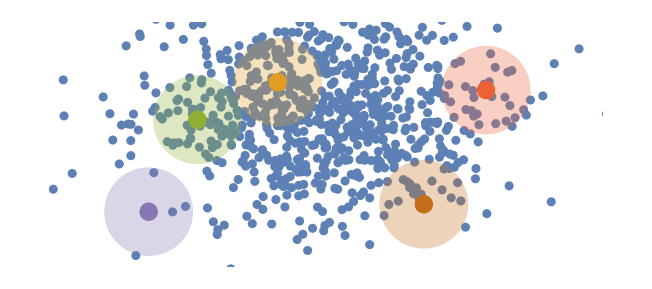

```mathematica
ptsplt=ListPlot[pts,PlotStyle->PointSize[0.01],Ticks->None,Axes->None,AspectRatio->8/18,PlotRange->{{-8,10},{-4,4}}];
ctrplt=ListPlot[Join[{{centers[[1]]}},Table[{centers[[i]]},{i,Length[centers]}]],PlotStyle->{PointSize[0.02]}];
circles=Table[Graphics[{ColorData[97,"ColorList"][[i+1]],Opacity[0.3],Disk[centers[[i]],windowSize]}],{i,Length[centers]}];
Show[ptsplt,ctrplt,circles]
```

## Iterate until convergence

```mathematica
IsInWindow[center_,p_,r_]:=Return[Sum[(center[[i]]-p[[i]])^2,{i,Length[center]}]≤r];
```

```mathematica
maxIter=50;
centerPoss={centers};
For[iter=1,iter≤maxIter,iter++,
newCenterPos={};
For[c=1,c≤Length[centers],c++,
internal={};
For[p=1,p≤Length[pts],p++,
If[IsInWindow[centers[[c]],pts[[p]],windowSize],AppendTo[internal,pts[[p]]]];
];
If[Length[internal]≠0,
AppendTo[newCenterPos,Plus@@internal/Length[internal]];
];
];
centers=newCenterPos;
AppendTo[centerPoss,newCenterPos];
];
```

## Plot the paths of the sliding windows

```mathematica
trajectories=Table[Table[centerPoss[[i,j]],{i,Length[centerPoss]}],{j,Length[centerPoss[[i]]]}];
traj=Show[ListPlot[Table[trajectories[[i]],{i,Length[trajectories]}],PlotStyle->{PointSize[0.01]},Ticks->None,AspectRatio->4/10],Graphics[Join[{Thickness[0.01]},Table[{ColorData[97,"ColorList"][[i+1]],Opacity[0.7],Line[trajectories[[i]]]},{i,Length[trajectories]}]]]
];
```

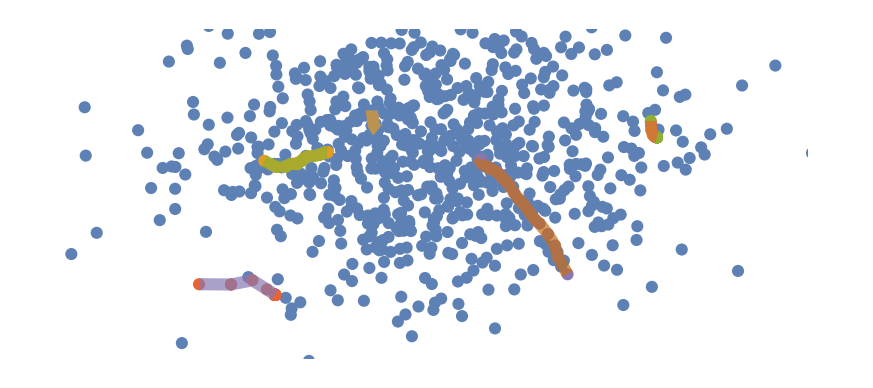

```mathematica
Show[ptsplt,traj]
```

## Animate the paths of the sliding windows

```mathematica
pics={};
For[cent=1,cent≤Length[centerPoss],cent++,
centers=centerPoss[[cent]];
ptsplt=ListPlot[pts,PlotStyle->PointSize[0.01],Ticks->None,Axes->None,AspectRatio->8/18,PlotRange->{{-8,10},{-4,4}}];
ctrplt=ListPlot[Join[{{centers[[1]]}},Table[{centers[[i]]},{i,Length[centers]}]],PlotStyle->{PointSize[0.02]}];
circles=Table[Graphics[{ColorData[97,"ColorList"][[i+1]],Opacity[0.3],Disk[centers[[i]],windowSize]}],{i,Length[centers]}];
AppendTo[pics,Show[ptsplt,ctrplt,circles]];
];
```

```mathematica
Export[NotebookDirectory[]<>"Mean-shift.gif",pics,"AnimationRepetitions"->∞,AnimationRate->0.5];
```